```mathematica
(*试图解决圆与椭圆相切的问题，答案倒是能暴力搞出来，但好像始终不优雅*)
```

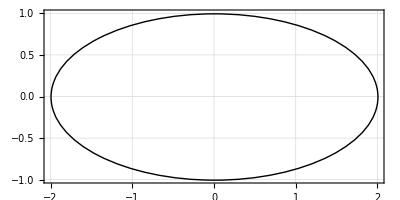

```mathematica
Graphics[Circle[{0,0},{2,1}],Frame->True,GridLines->Automatic,PlotRange->{{-2,2},{-1,1}}]
```

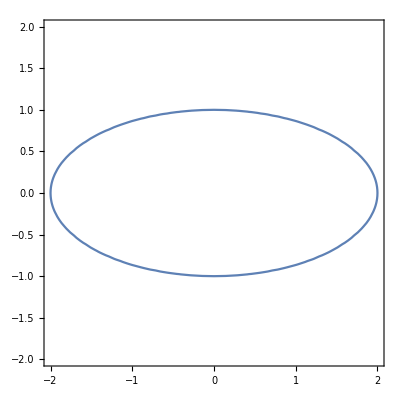

```mathematica
ContourPlot[x^2/4+y^2/1==1,{x,-2,2},{y,-2,2}]
```

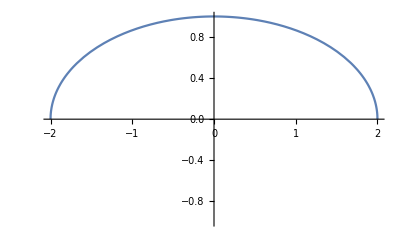

```mathematica
Plot[√(1-x^2/4),{x,-2,2},PlotRange->{{-2,2},{-1,1}}]
```

```mathematica
pX=Solve[D[√(1-x^2/4),x]==-1,x]//Flatten//x/.#&
```

4/(√5)

```mathematica
pY=√(1-x^2/4)/.x->pX
```

1/(√5)

```mathematica
p={circleX,circleY}
```

{4/(√5),1/(√5)}

```mathematica
distance[{x1_,y1_},{x2_,y2_}]:=√((x1-x2)^2+(y1-y2)^2);
```

```mathematica
r=1/2 distance[p,{2,1}]
```

1/2 √((-1+1/(√5))^2+(-2+4/(√5))^2)

```mathematica
r//FullSimplify
```

√(3/10 (7-3 √5))

```mathematica
r//N
```

0.29587

```mathematica
Manipulate[
Graphics[{
Circle[{0,0},{2,1}],
Point[{4/(√5),1/(√5)}],
Circle[{2-r,1-r},r],
Line[{{0,-1},{2,1}}]
},Frame->True,GridLines->Automatic,PlotRange->{{-2,2},{-1,1}}],
{r,0,1}
]
```

```mathematica
Solve[(x-2+r)^2+(y-1+r)^2==r^2,y]
```

{{y→1-r-√(-4+4 r+4 x-2 r x-x^2)},{y→1-r+√(-4+4 r+4 x-2 r x-x^2)}}

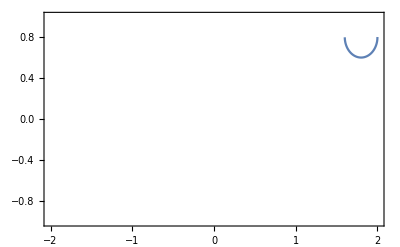

```mathematica
Plot[1-r-√(-4+4 r+4 x-2 r x-x^2)/.r->0.2,{x,-2,2},PlotRange->{{-2,2},{-1,1}},Frame->True]
```

```mathematica
Solve[1-r-√(-4+4 r+4 x-2 r x-x^2)==√(1-x^2/4),x,Assumptions->{x∈Reals,r∈Reals}]//FullSimplify
```

```mathematica
{{x->ConditionalExpression[-2/3 (-4-√2 (-1+r)+2 r+√(-6+4 √2+r (10-6 √2+(-3+2 √2) r))), √3+√6+r>3+√2&&1/(√2)+r<1]},{x->ConditionalExpression[2/3 (4-√2+(-2+√2) r+√(-6+4 √2+r (10-6 √2+(-3+2 √2) r))), ]},{x->ConditionalExpression[2/3 (4-√2+(-2+√2) r+√(-6+4 √2+r (10-6 √2+(-3+2 √2) r))), √2+√6+r>3+√3&&r<1]}}
```

```mathematica
Reduce[√3+√6+r>3+√2&&1/(√2)+r<1,r]
```

3+√2-√3-√6<r<1/2 (2-√2)

3+√2-√3 (1+√2)

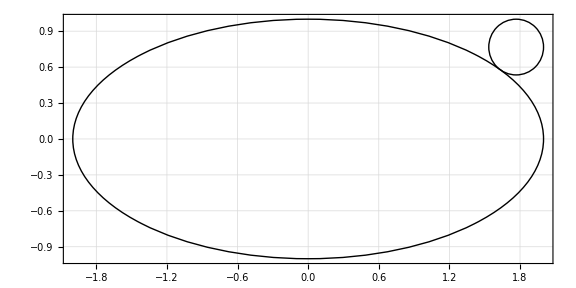

```mathematica
r=3+√2-√3-√6//FullSimplify
Graphics[{
Circle[{0,0},{2,1}],
Circle[{2-r,1-r},r]
},Frame->True,GridLines->Automatic,PlotRange->{{-2,2},{-1,1}},ImageSize->Large]
```

```mathematica
s=Solve[1-r-√(-4+4 r+4 x-2 r x-x^2)==√(1-x^2/4),x];
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

```mathematica
Reduce[
Module[{a},
a=({x,x,x,x}/.s);
{
a∈Reals,
r>0
}
]
,r]//FullSimplify
```

(√2+√6+r≥3+√3&&r<1)||(r>1&&√2+√3+r≤3+√6)

```mathematica
s=Solve[1-r-√(-4+4 r+4 x-2 r x-x^2)==√(1-x^2/4)/.r->3+√2-√3 (1+√2),x]//Flatten//{x,x}/.#&;
```

```mathematica
s[[1]]-s[[2]]//N
```

0.

```mathematica
s//N
```

{1.63299-4.09931×10^-6 ⅈ,1.63299-4.09931×10^-6 ⅈ}

```mathematica
s[[1]]==s[[2]]//Simplify
```

True

```mathematica
Reduce[
Length@Solve[1-r-√(-4+4 r+4 x-2 r x-x^2)==√(1-x^2/4),x]==2,
r
]
```